```mathematica
InsideBar[{x_,y_}]:=Abs[y]<1.5&&Abs[x]≤6.5
```

```mathematica
InsideInnerSign[{x_,y_}]:=Norm[{x,y}]≤7.5&&!InsideBar[{x,y}]
```

```mathematica
InsideOuterRing[{x_,y_}]:=7.5<Norm[{x,y}]<7.8
```

```mathematica
InsideNoEntrySign[{x_,y_}]:=Norm[{x,y}]<7.8
```

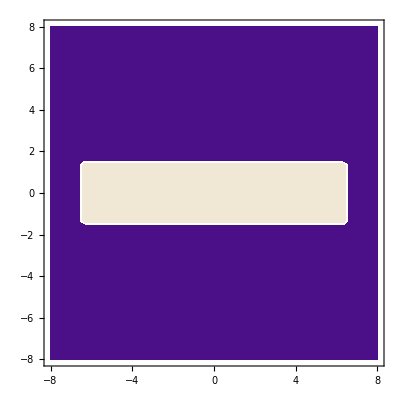
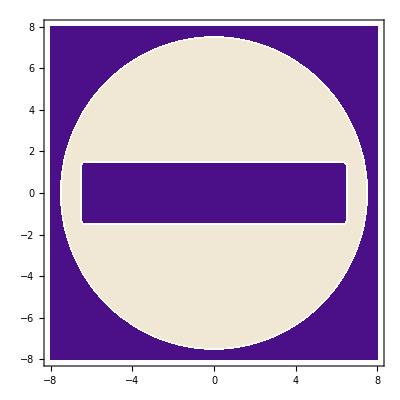
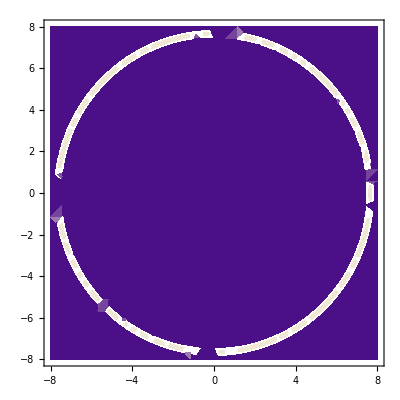
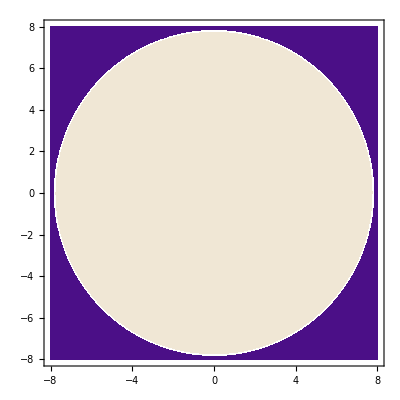

```mathematica
Map[DensityPlot[Boole[#[{x,y}]],{x,-8,+8},{y,-8,+8}]&,{InsideBar,InsideInnerSign,InsideOuterRing,InsideNoEntrySign}]
```

```mathematica
ptchMonte=Table[{Random[],Random[]}-{0.5,0.5},{40}];
```

```mathematica
transform[{px_,py_},{s_,mx_,my_}]:={
Total[Map[1-Boole[InsideNoEntrySign[({px,py}+#+{mx,my})*s]]&,ptchMonte]]/40.,
Total[Map[Boole[InsideInnerSign[({px,py}+#+{mx,my})*s]]&,ptchMonte]]/40.,
Total[Map[Boole[InsideOuterRing[({px,py}+#+{mx,my})*s]]+Boole[InsideBar[({px,py}+#+{mx,my})*s]]&,ptchMonte]]/40.
}
```

```mathematica
w=Integrate[PDF[UniformDistribution[{0,f1}],x-z] PDF[NormalDistribution[.3 f2 b1+ .95 f3 b1,Sqrt[(.1)^2 f2^2 + (.1)^2 f3^2]],z],
{z,-∞,+∞}]
```

Piecewise[{{(0.5 (-6. b1 f2 √((20. f1+6. b1 f2+19. b1 f3-20. x)^2/(f2^2+f3^2)) Erf[0.353553 √((6. b1 f2+19. b1 f3-20. x)^2/(f2^2+f3^2))]-19. b1 f3 √((20. f1+6. b1 f2+19. b1 f3-20. x)^2/(f2^2+f3^2)) Erf[0.353553 √((6. b1 f2+19. b1 f3-20. x)^2/(f2^2+f3^2))]+20. √((20. f1+6. b1 f2+19. b1 f3-20. x)^2/(f2^2+f3^2)) x Erf[0.353553 √((6. b1 f2+19. b1 f3-20. x)^2/(f2^2+f3^2))]+20. f1 √((6. b1 f2+19. b1 f3-20. x)^2/(f2^2+f3^2)) Erf[0.353553 √((20. f1+6. b1 f2+19. b1 f3-20. x)^2/(f2^2+f3^2))]+6. b1 f2 √((6. b1 f2+19. b1 f3-20. x)^2/(f2^2+f3^2)) Erf[0.353553 √((20. f1+6. b1 f2+19. b1 f3-20. x)^2/(f2^2+f3^2))]+19. b1 f3 √((6. b1 f2+19. b1 f3-20. x)^2/(f2^2+f3^2)) Erf[0.353553 √((20. f1+6. b1 f2+19. b1 f3-20. x)^2/(f2^2+f3^2))]-20. √((6. b1 f2+19. b1 f3-20. x)^2/(f2^2+f3^2)) x Erf[0.353553 √((20. f1+6. b1 f2+19. b1 f3-20. x)^2/(f2^2+f3^2))]))/(f1 √(f2^2+f3^2) √((6. b1 f2+19. b1 f3-20. x)^2/(f2^2+f3^2)) √((20. f1+6. b1 f2+19. b1 f3-20. x)^2/(f2^2+f3^2))), f1>0.}, {0., True}}]

```mathematica
pyrs=Map[BuildPyramid,positives];
```

```mathematica
candList=Select[Import["C:\\Users\\Julian\\secure\\Shape Recognition\\Stop Sign\\Positions.wdx"],InBoundsQ[pyrs[[1]],#[[2]],#[[3]],#[[4]]]&];
```

```mathematica
patches=Map[Patch[pyrs[[#[[1]]]],#[[2]],#[[3]],#[[4]]]&,candList];
```

```mathematica
probDens[v_,{f1_,f2_,f3_}]:=(0.5 (-1. Erf[(0.7071067811865475 (8. f2+19. f3-20. v))/(√(f2^2+f3^2))]+Erf[(0.7071067811865475 (20. f1+8.f2+19. f3-20.v))/(√(f2^2+f3^2))]))/f1
```

```mathematica
probDens[v_,{f1_,f2_,f3_},br_]=(w /. x->v /. b1->br);
```

```mathematica
LogSum[l1_,l2_]:=Max[l1,l2]+Log[Exp[l1-Max[l1,l2]]+Exp[l2-Max[l1,l2]]]
```

```mathematica
toDisk:={{1,0,0},{0,1,1},{0,0,0}};
```

```mathematica
NoEntrySignPatch[patch_,b_,{s_,mx_,my_}]:=
Log[Product[Max[probDens[patch[[y+9,x+9]],transform[{x,y},{s,mx,my}]+{1,1,1}*.01,b],.001],{y,-8,+8},{x,-8,8}]]-
LogSum[3.1 π s^2,Log[Product[Max[probDens[patch[[y+9,x+9]],toDisk.transform[{x,y},{s,mx,my}]+{1,1,1}*.01,b],.001],{y,-8,+8},{x,-8,8}]]]
```

```mathematica
NoEntrySignPatch[patch_]:=.1*Sum[NoEntrySignPatch[patch,b,{s,mx,my}],{b,0.1,1,.1},{s,0.8,1.2,0.1},{mx,-2,2,0.5},{my,-.5,+.5,0.5}]
```

```mathematica
NoEntrySignPatchDiag[patch_]:=.1*Table[NoEntrySignPatch[patch,b,{s,mx,my}],{b,0.3,.45,.05},{s,0.8,1.3,0.1},{mx,-2,2,0.5},{my,-.5,+.5,0.5}]
```

```mathematica
NoEntrySignPatch[patch_]:=
.1*Sum[Exp[.1*
Sum[
If[InsideBar[{x,y},0],Log[1/(√(2 π) .05)]-(patch[[y+9,x+9]]-0.95*b)^2/(2 (.05)^2),0]+
If[InsideInnerSign[{x,y},0],Log[1/(√(2 π) .05)]-(patch[[y+9,x+9]]-0.4*b)^2/(2 (.05)^2),0]
,{y,-8,+8},{x,-8,+8}]],{b,0,1,0.1}]
```

```mathematica
FilterOutput[image_,pyr_,res1_]:=(
rnk=20.;
focus=Position[res1,x_/;x≥rnk];
focus=Select[focus,InBoundsQ[pyr,#[[1]],#[[2]],#[[3]]]&];

res2=res1*.0;
res3=ReplacePart[res2,
Map[#->NoEntrySignPatch[Patch[pyr,#[[1]],#[[2]],#[[3]]]]&,focus]];
Show[image//DispImage,BoundingRectangles[res3,12000.,{8,8}]//OutlineGraphics]  )
```

```mathematica
NoEntryRecognitionOutput1[image_]:=(
res=NoEntryRecognition[image];
FilterOutput[image])
```

```mathematica
b*.95
```

0.353772

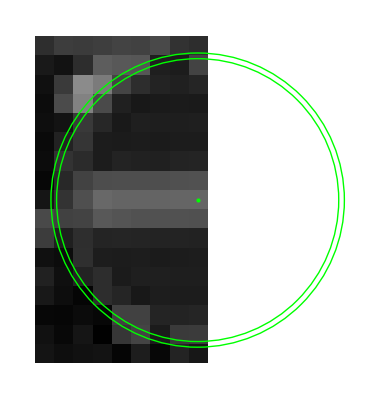
{-441.048,-Graphics-,(0.978 | 0.978 | 0.978 | 0.978 | 0.978 | 0.978 | 0.978 | 1.060 | 1.080
0.978 | 0.978 | 0.978 | 0.978 | 1.080 | 1.480 | -6.910 | -6.360 | 0.075
0.978 | 0.978 | -6.910 | 1.240 | -0.750 | 0.445 | -0.188 | -0.350 | -0.009
0.978 | 0.978 | 0.749 | 0.785 | -0.364 | -0.988 | -0.817 | -0.773 | -0.843
0.978 | -6.910 | -0.957 | 0.111 | -0.932 | -0.481 | -0.549 | -0.527 | -0.458
0.978 | -6.910 | 0.810 | -0.701 | -0.754 | -0.707 | -0.742 | -0.650 | -0.657
0.978 | -1.010 | 0.325 | -0.682 | -0.186 | -0.307 | -0.349 | -0.193 | -0.101
-6.910 | -4.320 | -6.910 | -6.910 | -6.910 | -6.910 | -6.910 | -6.910 | -6.910
-6.910 | -0.869 | -6.910 | -6.910 | -6.910 | -6.910 | -6.910 | -6.910 | -6.910
1.140 | -0.112 | -6.910 | -6.910 | -6.910 | -6.910 | -6.910 | -6.910 | -6.910
0.978 | -6.910 | 0.480 | -0.082 | -0.030 | -0.099 | -0.144 | -0.189 | -0.219
0.978 | -6.910 | 0.552 | -0.604 | -0.644 | -0.586 | -0.739 | -0.655 | -0.571
0.978 | -6.910 | -4.610 | 0.444 | -0.725 | -0.433 | -0.475 | -0.523 | -0.500
0.978 | 0.978 | -6.910 | -0.529 | -0.011 | -1.020 | -0.618 | -0.704 | -0.668
0.978 | 0.978 | 0.978 | -6.910 | -2.260 | 1.190 | -0.117 | -0.192 | -0.049
0.978 | 0.978 | 0.978 | -6.910 | 1.120 | -4.010 | -6.910 | -0.303 | 0.160
0.978 | 0.978 | 0.978 | 0.978 | 0.978 | 0.978 | 0.978 | 1.060 | -5.680),(0.084 | 0.201 | 0.310 | 0.407 | 0.392 | 0.391 | 0.391 | 0.396 | 0.396
0.285 | 0.254 | 0.262 | 0.346 | 0.328 | 0.319 | 0.319 | 0.318 | 0.315
0.234 | 0.123 | 0.179 | 0.142 | 0.145 | 0.141 | 0.138 | 0.136 | 0.134
0.065 | 0.049 | 0.185 | 0.113 | 0.111 | 0.114 | 0.107 | 0.111 | 0.115
0.129 | 0.058 | 0.137 | 0.177 | 0.107 | 0.122 | 0.120 | 0.118 | 0.119
0.096 | 0.050 | 0.021 | 0.176 | 0.146 | 0.093 | 0.113 | 0.108 | 0.110
0.026 | 0.023 | 0.044 | 0.029 | 0.254 | 0.253 | 0.140 | 0.136 | 0.144
0.065 | 0.031 | 0.084 | 0.005 | 0.210 | 0.267 | 0.105 | 0.226 | 0.231
0.080 | 0.056 | 0.068 | 0.073 | 0.021 | 0.113 | 0.028 | 0.138 | 0.090)}

```mathematica
pt=patches[[3]];{
b=loc[[1]];
s=loc[[2]];
mx=loc[[3]];
my=loc[[4]];
NoEntrySignPatch[pt,b,{s,mx,my}],
Show[{
pt[[1;;17,1;;9]]//DispImage,
OutlineGraphics[{Rectangle[({-6.5,-1.5}-{mx,my})/s+{8.5,8.5},({6.5,1.5}-{mx,my})/s+{8.5,8.5}],
}
],
{Green,
Circle[{8.5,8.5}-{mx,my},7.5/s],
Circle[{8.5,8.5}-{mx,my},7.8/s],
Point[{0,0}+{8.5,8.5}]}//Graphics
}],
NumberForm[(w2=Log[Table[
Max[probDens[pt[[y+9,x+9]],transform[{x,y},{s,mx,my}]+{1,1,1}*.01,b],.001]
,{y,-8,+8},{x,-8,+0}]])//Reverse//MatrixForm,{3,3}],NumberForm[pt[[1;;9,1;;9]]//Reverse//MatrixForm,{3,3}]}
```

```mathematica
baseParams={0.5,1.0,0.0,0.0};
```

```mathematica
GradientShape1[patch_,{b_,s_,x_,y_}]:=
(gr={
NoEntrySignPatch[patch,b+.01,{s,x,y}]-
NoEntrySignPatch[patch,b,{s,x,y}],
NoEntrySignPatch[patch,b,{s+.1,x,y}]-
NoEntrySignPatch[patch,b,{s,x,y}],
NoEntrySignPatch[patch,b,{s,x+.1,y}]-
NoEntrySignPatch[patch,b,{s,x,y}],
NoEntrySignPatch[patch,b,{s,x,y+.1}]
-NoEntrySignPatch[patch,b,{s,x,y}]
}*{100,10,10,10})
```

```mathematica
GradientAscent[patch_,iter_:20]:=(For[t6=1;loc=baseParams,t6≤iter,t6=t6+1,(tmp=8;loc=0.01*Normalize[GradientShape1[patch,loc]]+loc;
r=4;
val=NoEntrySignPatch[patch,loc[[1]],{loc[[2]],loc[[3]],loc[[4]]}]
)
];val)
```